-6.29145-8.61826 ⅈ

-9.91411+6.95535 ⅈ

122.317+41.6832 ⅈ

0.946548+0.322564 ⅈ

{{0.946548,0.322564},{0.946404,0.322985},{{0.946548,0.322564}}}

t/(1+(9 t^2)/32)

{{0.946548,0.322564},{0.946404,0.322985},{{0.946548,0.322564}},{{0.946404,0.322985}}}

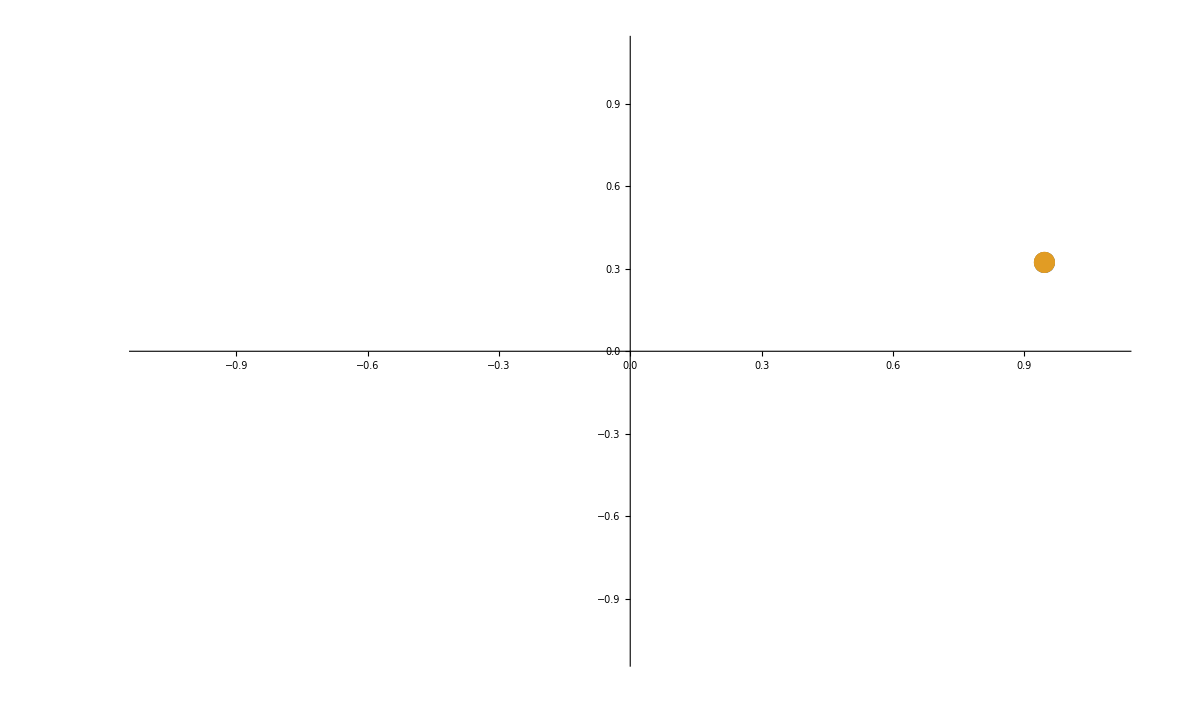

```mathematica
ClearAll["Global`*"];

atan[x_]:=x/(1+(9/32)x^2);
atan2[fun_, x_,y_] :=  Evaluate[Piecewise[{
{2*fun[y/(x+Sqrt[x^2+y^2])], x > 0},
{2*fun[(Sqrt[x^2+y^2] -x)/y], x <= 0 && y !=0},
{Pi, x <0 && y ==0}
}]]

v=RandomComplex[{-10-10I,10+10 I}]
w = RandomComplex[{-10-10I,10+10 I}]
zz = v*w
z =Normalize[zz]
zr = Re[z];
zj = Im[z];
max = Max[zr, zj];
min = Min[zr, zj];
r = Sqrt[zr^2+zj^2];
f[x_] := (x - min) / (max - min);

a = ArcTan[zr, zj] //N;
(*atan2[ArcTan, zr,zj]  // N;*)
b = atan2[atan, zr,zj]  // N;
{a,b};
lst = (t|->{r*Cos[t], r*Sin[t]}) /@ %;

(*x = Re[zz]/(Norm[v]*Norm[w])*)
g[Z_, zed_, vee_] := x = Re[Z]/(Norm[zed]*Norm[vee]);

(*g[Z_, zed_, vee_] := x = Re[Z]/(Norm[zed]*Norm[vee]);
h[r_,t_]:={r*Sin[t], r*Cos[t]};
AppendTo[lst, h[r,g[zz, v, w]]]*)
(*AppendTo[lst, (t|->{r*Sin[t], r*Cos[t]})[g[zz, v, w]]]*)
f[t_] :=Evaluate[Normal[Series[ArcCos[1-t],{t,0,3}]]];
h[x_]:=f[1-x] // N
AppendTo[lst, (t|->{r*Cos[t], r*Sin[t]}) /@ {h[g[zz,v,w]]}]

(*Normal[Series[ArcCos[t],{t,0,3}]]
f[t_]:=Evaluate[%]
h[x_]:=f[1-x]
AppendTo[lst, (t|->{r*Cos[t], r*Sin[t]}) /@ {h[g[zz,v,w]]}]*)
atan[t]
f[t_,u_]:=Evaluate[FullSimplify[atan2[atan, t, u]]]

AppendTo[lst, (t|->{r*Cos[t], r*Sin[t]}) /@ {f[Re[zz],Im[zz]]}]
ListPlot[{{lst[[1]]},{lst[[2]]}}, PlotRange->{{-1.1,1.1}, {-1.1, 1.1}}]
```